## Otsuji model

## Comsol import

```mathematica
paramsOtsuji={Du->1,Dv->10,rhobar->10};
```

### Import Otsuji model simulation

```mathematica
fileOtsuji=NotebookDirectory[]<>"OtsujiModel-rhobar=10_0-L=1000-dx=0_1-seed=1-pbc.h5";
```

```mathematica
Import[fileOtsuji,"StructureGraph"]
```

-Graphics-

```mathematica
rhoOtsuji=Import[fileOtsuji,{"Data","data"}];
tOtsuji=Import[fileOtsuji,{"Data","times"}];
xOtsuji=Import[fileOtsuji,{"Data","grid"}];
```

```mathematica
rhoOtsujiRed=Mean[Transpose[Partition[#,5]]]&/@rhoOtsuji;
xOtsujiRed=Mean[Transpose[Partition[#,5]]]&@xOtsuji;
```

### Kymograph

```mathematica
ListDensityPlot[Log10@(1+rhoOtsujiRed),PlotRange->All,PlotLegends->Automatic,ColorFunction->(GrayLevel[1-#]&)]
```

-Graphics-

x goes in space from 0 to 1000

```mathematica
xOtsujiRed[[{1,-1}]]
```

{0.25,999.75}

t goes from 1 to 10^9

```mathematica
tOtsuji[[{1,-1}]]
```

{0.,1.×10^9}

### Peak profiles

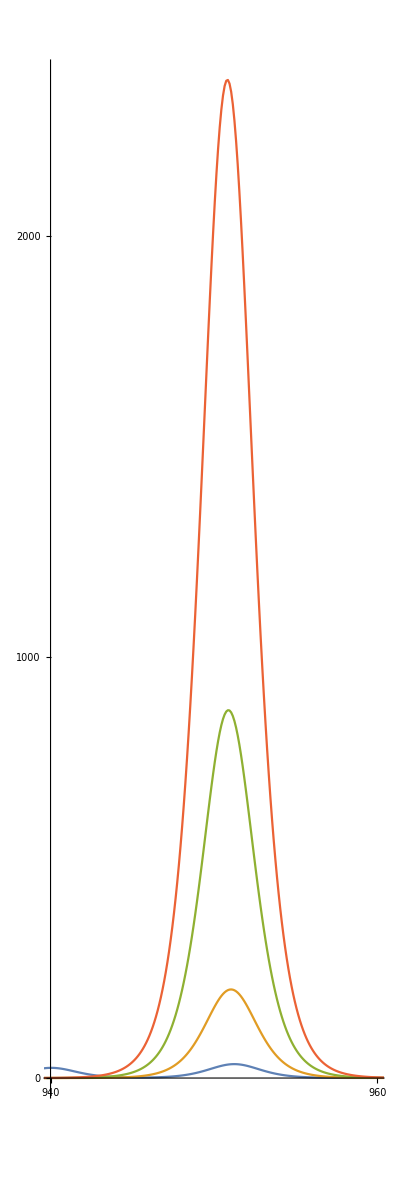

```mathematica
ListLinePlot[Transpose@{xOtsuji,rhoOtsuji[[#]]}&/@{32,52,72,92},PlotRange->{{940,960},All},PerformanceGoal->"Quality",Ticks->{{940,960},{0,1000,2000}},AspectRatio->3/1]
```

#### Stationary peak profile

from Ref. [26]

```mathematica
statOtsuji=M/(4Sqrt[Du/(1-Du/Dv)])*Sech[x/(2Sqrt[Du/(1-Du/Dv)])]^2;
```

```mathematica
massPosOtsuji={NIntegrate[Interpolation[Transpose@{xOtsuji,rhoOtsuji[[#]]}][x],{x,943,959},Method->"InterpolationPointsSubdivision"],x/.Last@FindMaximum[Interpolation[Transpose@{xOtsuji,rhoOtsuji[[#]]}][x],{x,950},Method->"Newton"]}&/@{32,52,72,92}
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{147.035,951.238},{890.943,951.041},{3690.49,950.883},{9989.93,950.818}}

```mathematica
Mean[massPosOtsuji[[All,2]]]
```

950.995

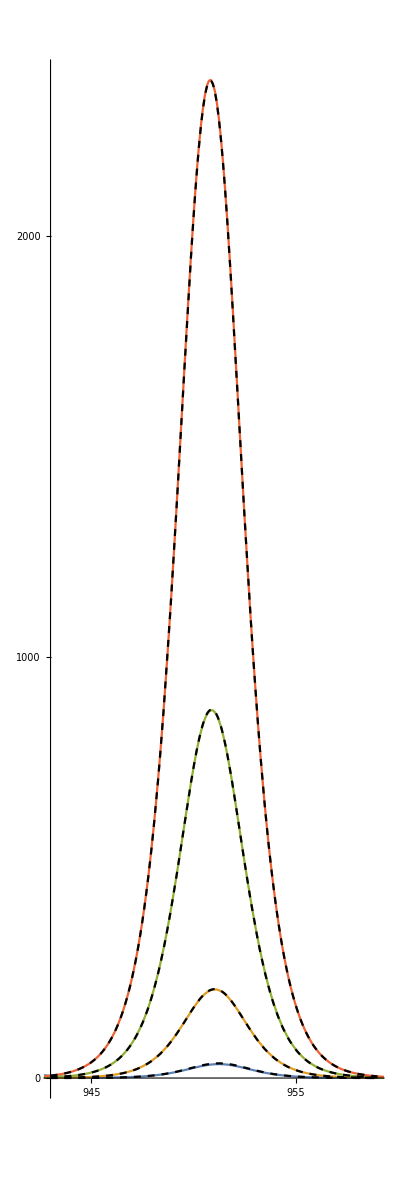

```mathematica
Show[ListLinePlot[Transpose@{xOtsuji,rhoOtsuji[[#]]}&/@{32,52,72,92},PlotRange->{{943,959},All},PerformanceGoal->"Quality",Ticks->{{945,955},{0,1000,2000}},AspectRatio->3/1],
Plot[(statOtsuji/.x->(xx-#[[2]])/.paramsOtsuji/.M->#[[1]])&/@massPosOtsuji,{xx,943,959},PlotStyle->{Black,Dashed},PlotRange->All]]
```

## Cubic model at rhobar=-0.2

## Comsol import

```mathematica
paramsCubic1={Du->1,Dv->10,rhobar->-0.2};
```

### Import cubic model simulation

```mathematica
fileCubic1=NotebookDirectory[]<>"cubicModel-rhobar=-0_2-L=1000-dx=0_5-seed=1-pbc.h5";
```

```mathematica
Import[fileCubic1,"StructureGraph"]
```

-Graphics-

```mathematica
rhoCubic1=Import[fileCubic1,{"Data","data"}];
tCubic1=Import[fileCubic1,{"Data","times"}];
xCubic1=Import[fileCubic1,{"Data","grid"}];
```

### Kymograph

```mathematica
ListDensityPlot[Transpose@rhoCubic1,PlotRange->All,PlotLegends->Automatic,ColorFunction->(GrayLevel[1-#]&)]
```

-Graphics-

x goes in space from 0 to 1000

```mathematica
xCubic1[[{1,-1}]]
```

{0.25,999.75}

t goes from 1 to 10^9

```mathematica
tCubic1[[{1,-1}]]
```

{1.,1.×10^10}

### Kink profile

```mathematica
statCubic=Tanh[x/(Sqrt[2Du])];
```

```mathematica
x01=x/.FindRoot[Interpolation[Transpose@{xCubic1,rhoCubic1[[31]]}][x],{x,7}]
```

7.52691

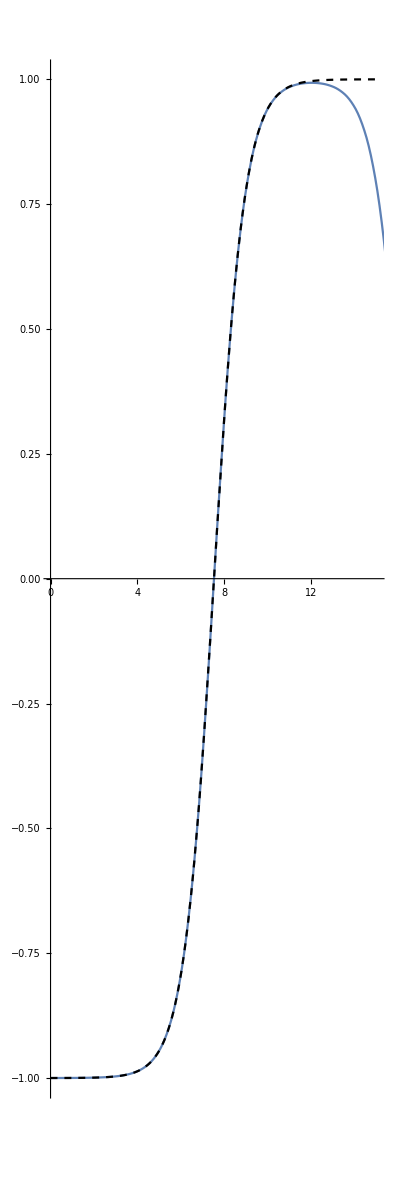

```mathematica
Show[ListLinePlot[Transpose@{xCubic1,rhoCubic1[[31]]},PlotRange->{{0,2x01},All},PerformanceGoal->"Quality",AspectRatio->3/1],
Plot[statCubic/.x->(xx-x01)/.paramsCubic,{xx,0,2x01},PlotStyle->{Black,Dashed},PlotRange->All]]
```

## Cubic model at rhobar=0.2

## Comsol import

```mathematica
paramsCubic2={Du->1,Dv->10,rhobar->0.2};
```

### Import cubic model simulation

```mathematica
fileCubic2=NotebookDirectory[]<>"cubicModel-rhobar=0_2-L=1000-dx=0_5-seed=1-pbc.h5";
```

```mathematica
Import[fileCubic2,"StructureGraph"]
```

-Graphics-

```mathematica
rhoCubic=Import[fileCubic2,{"Data","data"}];
tCubic=Import[fileCubic2,{"Data","times"}];
xCubic=Import[fileCubic2,{"Data","grid"}];
```

### Kymograph

```mathematica
ListDensityPlot[Transpose@rhoCubic,PlotRange->All,PlotLegends->Automatic,ColorFunction->(GrayLevel[1-#]&)]
```

-Graphics-

x goes in space from 0 to 1000

```mathematica
xCubic[[{1,-1}]]
```

{0.25,999.75}

t goes from 1 to 10^9

```mathematica
tCubic[[{1,-1}]]
```

{1.,1.×10^10}

### Kink profile

```mathematica
statCubic=Tanh[x/(Sqrt[2Du])];
```

```mathematica
x0=x/.FindRoot[Interpolation[Transpose@{xCubic,rhoCubic[[21]]}][x],{x,5}]
```

6.5729

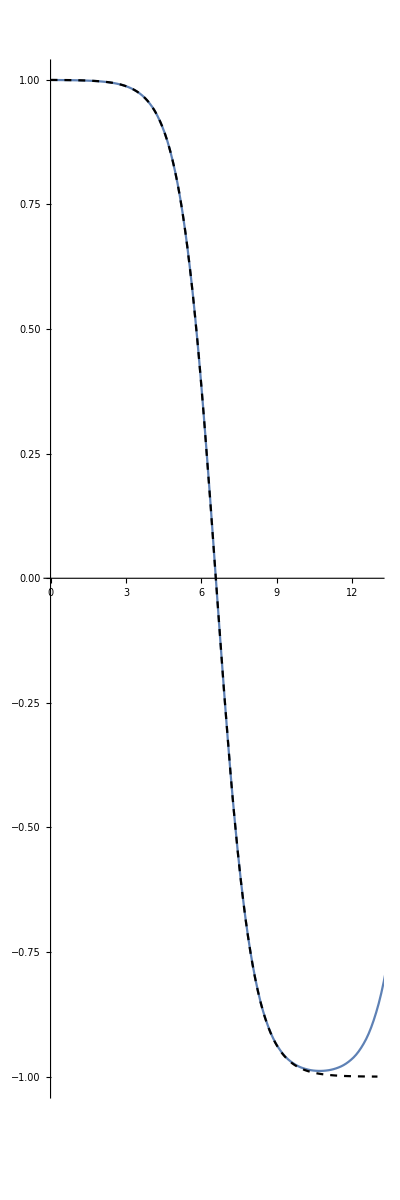

```mathematica
Show[ListLinePlot[Transpose@{xCubic,rhoCubic[[21]]},PlotRange->{{0,13},All},PerformanceGoal->"Quality",AspectRatio->3/1],
Plot[statCubic/.x->(-xx+x0)/.paramsCubic,{xx,0,13},PlotStyle->{Black,Dashed},PlotRange->All]]
```